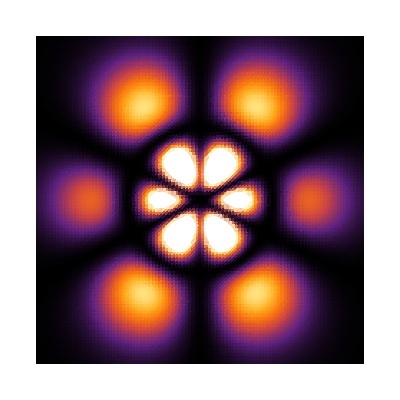

```mathematica
detail[n_,l_,m_]:=5Total@{n,l,m}
F[n_,l_,x_]:=x^l ⅇ^(-x/2)(n+l)!LaguerreL[n-l-1,2l+1,x]
R[n_,l_,r_,a_]:=(2/(n a))^2 √(a/4((n-l-1)!)/((n+l)!)^3)F[n,l,(2r)/(n a)]
Y[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ]
ψ[n_,l_,m_,r_,a_,θ_,ϕ_]:=R[n,l,r,a]Abs@Y[l,m,θ,ϕ]
orb[n_,l_,m_,x_,y_,z_]:=Module[{r=Norm@{x,y,z}},
ψ[n,l,m,r,y,ArcCos@(z/r),ArcTan[x,0]]^2]
orbDensity[n_,l_,m_]:=DensityPlot[orb[n,l,m,x,1,z],{x,-detail[n,l,m],detail[n,l,m]},{z,-detail[n,l,m],detail[n,l,m]},
Mesh->False,Frame->False,PlotPoints->100,ColorFunctionScaling->True,ColorFunction->"SunsetColors"]
orbDensity[5,3,1]
```